## Figure 4

```mathematica
path=NotebookDirectory[];
```

### Comparing absolute time between distortion based drive and viability (Medea)

```mathematica
distortondata=Import[path<>"/Tcrit_distortion_no_cost_new.txt","CSV"];
medeadata=Import[path<>"/Tcrit_medea_no_cost_new.txt","CSV"];
```

```mathematica
distortionmatrix=distortondata⟦2;;,2;;⟧;
medeamatrix=medeadata⟦2;;,2;;⟧;
```

```mathematica
Dimensions[distortionmatrix]
```

{50,5}

```mathematica
Dimensions[medeamatrix]
```

{99,5}

```mathematica
topldistort=distortondata⟦{11,21,31,41,51}⟧
```

{{0.6,70.35,35.18,23.45,17.59,14.07},{0.7,36.96,18.48,12.32,9.24,7.4},{0.8,26.27,13.14,8.76,6.57,5.26},{0.9,21.23,10.62,7.08,5.31,4.25},{1,18.39,9.2,6.13,4.6,3.68}}

```mathematica
{11,21,31,41,51}+1
```

{12,22,32,42,52}

```mathematica
toplmedea=medeadata⟦{10,20,30,40,50,60,70,80,90,100}⟧
```

{{0.1,519.8,260,173.4,130,104},{0.2,253.8,127,84.6,63.6,50.8},{0.3,165,82.6,55,41.4,33},{0.4,120.2,60.2,40.2,30.2,24.2},{0.5,93.4,46.8,31.2,23.4,18.8},{0.6,75.2,37.6,25.2,18.8,15.2},{0.7,62,31,20.8,15.6,12.4},{0.8,52,26,17.4,13,10.4},{0.9,44.2,22.2,14.8,11.2,9},{1,38.4,19.2,12.8,9.6,7.8}}

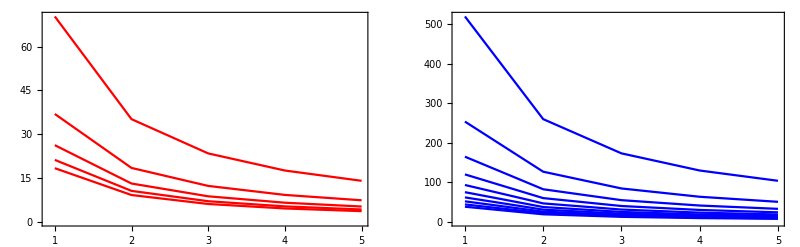

```mathematica
GraphicsRow[{ListPlot[topldistort⟦All,2;;⟧,Joined->True,PlotRange->All,PlotStyle->Red,Frame->True],ListPlot[toplmedea⟦All,2;;⟧,Joined->True,PlotRange->All,PlotStyle->Blue,Frame->True]}]
```

### Tcrit distortion cost

```mathematica
data=Import[path<>"/Tcrit_distortion_cost_new.txt","CSV"];
```

```mathematica
matrix=data⟦2;;,2;;⟧;
```

```mathematica
rescaledbymonogamy=Table[matrix⟦i⟧/matrix⟦i,1⟧,{i,1,Length[matrix],1}];
```

```mathematica
yrange=Table[{i,data⟦i+1,1⟧},{i,1,Length[data⟦All,1⟧]-1,4}];
yrange⟦All,2⟧=yrange⟦All,2⟧//Reverse
```

{0.995,0.955,0.915,0.875,0.835,0.795,0.755,0.715,0.675,0.635}

```mathematica
max=Reverse[rescaledbymonogamy]//Max
```

1.17251

```mathematica
min=Reverse[rescaledbymonogamy]//Min
```

0.344343

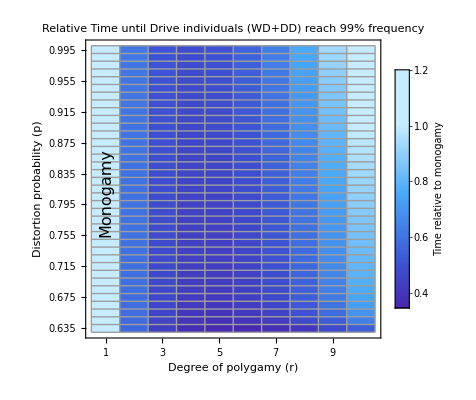

```mathematica
MatrixPlot[Reverse[rescaledbymonogamy],PlotRange->All,AspectRatio->1,ColorFunction->"DeepSeaColors",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"DeepSeaColors",{min,max+0.03}},LegendMarkerSize->250,LegendLabel->Placed[Rotate[Style["Time relative to monogamy",16],90 Degree],Right]],Automatic],FrameTicksStyle->Directive[Black,12],FrameTicks->{yrange,All},PlotLabel->Style["Relative Time until Drive individuals\n (WD+DD) reach 99% frequency",Black,18],FrameLabel->{Style["Distortion probability (p)",Black,16],Style["Degree of polygamy (r)",Black,16]},Epilog->{Inset[Rotate[Style["Monogamy",16,Black],90 Degree],{0.5,18}]},Mesh->True]
```

### Tcrit distortion no cost

```mathematica
data=Import[path<>"/Tcrit_distortion_no_cost_new.txt","CSV"];
```

```mathematica
matrix=data⟦2;;,2;;⟧;
```

```mathematica
rescaledbymonogamy=Table[matrix⟦i⟧/matrix⟦i,1⟧,{i,1,Length[matrix],1}];
```

```mathematica
yrange=Table[{i,data⟦i+1,1⟧},{i,1,Length[data⟦All,1⟧]-1,4}];
yrange⟦All,2⟧=yrange⟦All,2⟧//Reverse
```

{0.99,0.95,0.91,0.87,0.83,0.79,0.75,0.71,0.67,0.63,0.59,0.55,0.51}

```mathematica
max=Reverse[rescaledbymonogamy]//Max
```

1.

```mathematica
min=Reverse[rescaledbymonogamy]//Min
```

0.2

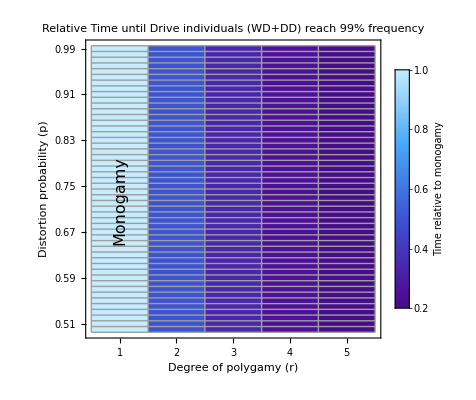

```mathematica
MatrixPlot[Reverse[rescaledbymonogamy],PlotRange->All,AspectRatio->1,ColorFunction->"DeepSeaColors",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"DeepSeaColors",{min,max}},LegendMarkerSize->250,LegendLabel->Placed[Rotate[Style["Time relative to monogamy",16],90 Degree],Right]],Automatic],FrameTicksStyle->Directive[Black,12],FrameTicks->{yrange,All},PlotLabel->Style["Relative Time until Drive individuals\n (WD+DD) reach 99% frequency",Black,18],FrameLabel->{Style["Distortion probability (p)",Black,16],Style["Degree of polygamy (r)",Black,16]},Epilog->{Inset[Rotate[Style["Monogamy",16,Black],90 Degree],{0.5,23}]},Mesh->True]
```

### Tcrit Medea no cost

```mathematica
data=Import[path<>"/Tcrit_medea_no_cost_new.txt","CSV"];
```

```mathematica
matrix=data⟦2;;,2;;⟧;
```

```mathematica
rescaledbymonogamy=Table[matrix⟦i⟧/matrix⟦i,1⟧,{i,1,Length[matrix],1}];
```

```mathematica
yrange=Table[{i,data⟦i+1,1⟧},{i,1,Length[data⟦All,1⟧]-1,6}];
yrange⟦All,2⟧=yrange⟦All,2⟧//Reverse
```

{0.98,0.92,0.86,0.8,0.74,0.68,0.62,0.56,0.5,0.44,0.38,0.32,0.26,0.2,0.14,0.08,0.02}

```mathematica
max=Reverse[rescaledbymonogamy]//Max
```

1.

```mathematica
min=Reverse[rescaledbymonogamy]//Min
```

0.2

```mathematica
MatrixPlot[Reverse[rescaledbymonogamy],PlotRange->All,AspectRatio->1,ColorFunction->"DeepSeaColors",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"DeepSeaColors",{min,max}},LegendMarkerSize->250,LegendLabel->Placed[Rotate[Style["Time relative to monogamy",16],90 Degree],Right]],Automatic],FrameTicksStyle->Directive[Black,12],FrameTicks->{yrange,All},PlotLabel->Style["Relative Time until Drive individuals\n (WD+DD) reach 99% frequency",Black,18],FrameLabel->{Style["Medea drive efficiency (d)",Black,16],Style["Degree of polygamy (r)",Black,16]},Epilog->{Inset[Rotate[Style["Monogamy",16,Black],90 Degree],{0.5,23}]},Mesh->True]
```